```mathematica
(*a set of observable transitions should read: { {{s(l), t(l), Subscript[r, l]}, {s(l̄), t(l̄), Subscript[r, l̄]}}, ... } *)
(*an event reads: x = {{s(l), t(l), Subscript[r, l]}, ...} for all l ∈ θ^-1 x*)

(*for aesthetic purposes, sorry*)
Needs["MaTeX`"]
SetDirectory[NotebookDirectory[]];
magentaviva = RGBColor[{190,52,85}/255];
pageantblue = RGBColor[{31,44,67}/255];
castletongreen = RGBColor[{28,88,64}/255];
sepia = RGBColor[{122,78,13}/255];
mark = #1 &@@@ Graphics`PlotMarkers[];
cross = Graphics[{Thickness[0.3],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];

(*stationary distribution achieved by a generator*)
SteadyState[mat_] := Module[{pss},
	pss = Table[(-1)^j Det[ Drop[mat,{2},{j}] ], {j,Length@mat}];
	pss = pss/Total[pss]
]

(*define log(0/0) = 0*)
SmartLog[a_, b_] := If[ PossibleZeroQ[Chop[a]] ∧ PossibleZeroQ[Chop[b]], 0, Log[a/b]]

(*entropy production rate, "set" has to include ALL transitions*)
EPR[R_, set_] := Module[{ps},
	ps = SteadyState[R];
	Sum[( ps[[s[[1,1]]]]s[[1,3]] - ps[[s[[2,1]]]]s[[2,3]] ) SmartLog[s[[1,3]], s[[2,3]]], {s,set}]
]

(*traffic of a set of transitions*)
Kfun[set_, pss_] := Total[#3 pss[[#1]] &@@@ Flatten[set,1]]

(*survival matrix*)
Smatrix[R_, set_] := Module[{S},
	S = R;
	( S[[#2,#1]] -= #3 ) &@@@ Flatten[set,1];
	S
]

(*matrix Γ of an event x*)
Γmatrix[x_, pss_] := Module[{Γ},
	Γ = (Table[0, {i,Length[pss]}, {j,Length[pss]}]);
	(Γ[[#2,#1]] += #3) &@@@ x;
	Kfun[{x},pss]^-1 Γ
]

(*convenient functions for the statistics of events*)
Px[pss_,transitions_,R_][x_] := Kfun[{x},pss]/Kfun[transitions,pss];
Px2Gx1[pss_,transitions_,R_][x1_,x2_] := -Kfun[{x2},pss]Total[Γmatrix[x2,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x1,pss].pss]
Px2tGx1[pss_,transitions_,R_][x1_,x2_,t_] := Kfun[{x2},pss]Total[Γmatrix[x2,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x1,pss].pss]

(*Fermi-Dirac statistics*)
FD[ϵ_,β_] := (1+Exp[β ϵ])^-1;
```

## example of functions usage

defining the double QD model

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={4,3.5,1,7};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,5};
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
σ= pss[[4]](w0100r1 Log[w0100r1/w0001r1]+w0100r2 Log[w0100r2/w0001r2]+w1000r3 Log[w1000r3/w0010r3]+w1000r4 Log[w1000r4/w0010r4])+pss[[3]](w0010r3 Log[w0010r3/w1000r3]+w0010r4 Log[w0010r4/w1000r4]+w1110r1 Log[w1110r1/w1011r1]+w1110r2 Log[w1110r2/w1011r2])+pss[[2]](w1011r1 Log[w1011r1/w1110r1]+w1011r2 Log[w1011r2/w1110r2]+w0111r3 Log[w0111r3/w1101r3]+w0111r4 Log[w0111r4/w1101r4])+pss[[1]](w0001r1 Log[w0001r1/w0100r1]+w0001r2 Log[w0001r2/w0100r2]+w1101r3 Log[w1101r3/w0111r3]+w1101r4 Log[w1101r4/w0111r4])//N;
```

entropy production rate

```mathematica
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
{σ,EPR[R,transitions]}
```

{15.2455,15.2455}

defining the multifilar events

```mathematica
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
```

survival matrix from the function and also from R - 𝒦 Γ

```mathematica
Smatrix[R,{x1plus}]//MatrixForm
(R-Kfun[{x1plus},pss]Γmatrix[x1plus, pss])-Smatrix[R,{x1plus}]//MatrixForm//Chop
```

(-11.774 | 10.4494 | 0. | 4.08787
9.55061 | -25.7811 | 0.146561 | 0.
0. | 15.3318 | -4.20039 | 16.4679
2.22336 | 0. | 3.53214 | -30.2445)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

sum of traffic rates is the total traffic rate

```mathematica
Total[Kfun[{#},pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
Kfun[transitions,pss]
```

9.64768

9.64768

State after an event

```mathematica
Γmatrix[x3minus,pss].pss
```

{0.20145,0.,0.,0.79855}

P(ℓ, t | x)

```mathematica
w1101r3 (MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss)[[1]]//Simplify
```

0.00943792 ⅇ^(-11.774 t)

P(x’, t | x)

```mathematica
Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2tGx1[pss,transitions,R][x3minus,x4plus,t]//Simplify//Chop
```

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

P (x' | x) and its normalization

```mathematica
-Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2Gx1[pss,transitions,R][x3minus,x4plus]
Total[-Kfun[{#},pss]Total[Γmatrix[#,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.504999

0.504999

1.

P (x)

```mathematica
Kfun[{x1plus},pss]/Kfun[transitions,pss]
Px[pss,transitions,R][x1plus]
Total[Kfun[{#},pss]/Kfun[transitions,pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.124621

0.124621

1.

P(x1, t1, x2, t2 | x0)

```mathematica
x0=x1plus;x1=x3plus;x2=x2minus;
w1011r2 (MatrixExp[t2 S][[2,2]])w1101r3 (MatrixExp[t1 S].Γmatrix[x0,pss].pss)[[1]]//N//Expand//Chop
Kfun[{x1},pss]Kfun[{x2},pss]Tr[Γmatrix[x2,pss].MatrixExp[t2 S].Γmatrix[x1,pss].MatrixExp[t1 S].Γmatrix[x0,pss].pss]//N//Expand//Chop
```

0.163177 2.71828^(-7.54093 t1-21.2179 t2)

0.163177 2.71828^(-7.54093 t1-21.2179 t2)

```mathematica
x0=x1plus;x1=x1minus;x2=x1plus;
w0100r1 (MatrixExp[t2 S][[4,4]])w0001r1 (MatrixExp[t1 S].Γmatrix[x0,pss].pss)[[1]]+w1110r1 (MatrixExp[t2 S][[3,3]])w1011r1 (MatrixExp[t1 S].Γmatrix[x0,pss].pss)[[2]]//N//Expand//Chop
Kfun[{x1},pss]Kfun[{x2},pss]Tr[Γmatrix[x2,pss].MatrixExp[t2 S].Γmatrix[x1,pss].MatrixExp[t1 S].Γmatrix[x0,pss].pss]//N//Expand//Chop
```

9.11692 2.71828^(-7.54093 t1-28.6943 t2)+1.54355 2.71828^(-21.2179 t1-14.5468 t2)

9.11692 2.71828^(-7.54093 t1-28.6943 t2)+1.54355 2.71828^(-21.2179 t1-14.5468 t2)

## DQD

### not randomized

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,transitions,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*σwt*)
σwt=Z NIntegrate[Sum[Px2tGx1[pss,Xspace,R][x1,x2,t]Px[pss,Xspace,R][x1]SmartLog[Px2tGx1[pss,Xspace,R][x1,x2,t],Px2tGx1[pss,Xspace,R][rev[x2],rev[x1],t]],{x1,Xspace},{x2,Xspace}],{t,0,∞}];

AppendTo[vec,Chop@{A12,A34,σ,σzk,σti,σwt}];
,{x,3,7,.3}]
```

```mathematica
cross=Graphics[{Thickness[0.1],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->15]},LegendMarkers->(mark[[1]])],LineLegend[{Dashed,castletongreen},{MaTeX["\\sigma_\\text{zk}",FontSize->15]},LegendMarkerSize->22],PointLegend[{castletongreen},{MaTeX["(\\sigma_\\text{wt} + \\sigma_\\text{zk})/2",FontSize->15]},LegendMarkers->(cross)]},1,Spacings->{0,-1}];
plotDDEPR=Show[
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->{Black,Thick},PlotRange->All],
ListPlot[{#1,#5}&@@@vec,PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],10}],
ListPlot[{#1,(#6+Total[#4])/2}&@@@vec,PlotStyle->{castletongreen,Opacity[.8]},PlotMarkers->{cross,11}],
(*ListLinePlot[{#1,Total[#4[[;;2]]]}&@@@vec,PlotStyle->{castletongreen,Dashed}],
ListLinePlot[{#1,Total[#4[[;;4]]]}&@@@vec,PlotStyle->{castletongreen,Dotted}],*)
ListLinePlot[{#1,Total[#4[[;;6]]]}&@@@vec,PlotStyle->{castletongreen,Dashed}],
(*ListLinePlot[{#1,Total[#4[[;;8]]]}&@@@vec,PlotStyle->{castletongreen}],*)
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.5,.3}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->All,ImagePadding->{{25,5},{40,5}}]
```

-Graphics-

```mathematica
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->12]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->12]},LegendMarkers->(mark[[1]])],PointLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{A,B}",FontSize->12]},LegendMarkers->(mark[[2]])]},1,Spacings->{0,-1}];
plotBrussEPR=Show[{ListLinePlot[{#1,#2}&@@@data,PlotStyle->Black],
ListPlot[{#1,Around[#8,#9]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],11}],
ListPlot[{#1,Around[#6,#7]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],11}]},
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->12],""},Epilog->{Inset[leg,Scaled[{.6,.7}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-.42,.42},All},ImagePadding->{{25,5},{40,5}}]
```

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec2={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,Xspace,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*observing reservoir 1*)
trans1={x1plus,x1minus};
Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,trans1,R][x1,x2]Px[pss,trans1,R][x1];
Px2rx1r=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]Px[pss,trans1,R][rev[x2]];
a=Px2Gx1[pss,trans1,R][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,trans1,R][x1,x2,t])/a//Simplify//Chop];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,trans1,R][rev[x2],rev[x1],t])/b//Simplify//Chop];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;2]]},{x2,Xspace[[;;2]]}];

AppendTo[vec2,Chop@{A12,A34,σ,σzk,σti,Dx,Dtt}];
,{x,4.5,5.5,.025}]
```

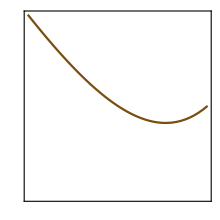
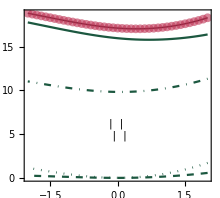
{-Graphics--Graphics-,-Graphics-}

```mathematica
size=220;ar=1;
leg=Column[{LineLegend[{pageantblue,sepia},MaTeX[#,FontSize->14]&/@{"D_x","D_t\\ [10^{-4}]"}]},Automatic,-.3];
plot1=ListLinePlot[{#1,#6}&@@@vec2,PlotStyle->pageantblue,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.6,.77}]]}];
plot2=ListLinePlot[{#1,#7 10^4}&@@@vec2,PlotStyle->sepia,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""}];
plotDDD=Overlay[{plot1,plot2}];
{plotDDD,plotDDEPR}
```

```mathematica
Export["plot_DD_EPR.png",plotDDEPR,"PNG",ImageResolution->600]
Export["plot_DD_Dxt.png",plotDDD,"PNG",ImageResolution->600]
```

plot_DD_EPR.png

plot_DD_Dxt.png

### randomized

```mathematica
{β1,β2,β3,β4}={1,1,1,1};
vec={};Do[
{Γ1,Γ2,Γ3,Γ4,μ1,μ2,μ3,μ4,ϵu,ϵd,Δϵ}=RandomReal[{1,5},11];
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
Xspace2=Xspace[[;;6]];
Z2=N@Kfun[Xspace2,pss];
σzk=Total[Z2( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace2];

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,transitions,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*σwt*)
Xspace2=Xspace[[;;6]];
Z2=N@Kfun[Xspace2,pss];
σwt=Z2 NIntegrate[Sum[Px2tGx1[pss,Xspace2,R][x1,x2,t]Px[pss,Xspace2,R][x1]SmartLog[Px2tGx1[pss,Xspace2,R][x1,x2,t],Px2tGx1[pss,Xspace2,R][rev[x2],rev[x1],t]],{x1,Xspace2},{x2,Xspace2}],{t,0,∞}];

(*Dx and Dt*)
Xspace3=Xspace[[;;2]];
Dx=Sum[Px2Gx1[pss,Xspace3,R][x1,x2]Px[pss,Xspace3,R][x1]SmartLog[Px2Gx1[pss,Xspace3,R][x1,x2]Px[pss,Xspace3,R][x1],Px2Gx1[pss,Xspace3,R][rev[x2],rev[x1]]Px[pss,Xspace3,R][rev[x2]]],{x1,Xspace3},{x2,Xspace3}];
DDt=Sum[Px2Gx1[pss,Xspace3,R][x1,x2]Px[pss,Xspace3,R][x1]Quiet@NIntegrate[
(Px2tGx1[pss,Xspace3,R][x1,x2,t])/(Px2Gx1[pss,Xspace3,R][x1,x2])SmartLog[
Px2tGx1[pss,Xspace3,R][x1,x2,t]Px2Gx1[pss,Xspace3,R][rev[x2],rev[x1]],
Px2Gx1[pss,Xspace3,R][x1,x2]Px2tGx1[pss,Xspace3,R][rev[x2],rev[x1],t]
]
,{t,0,∞}],{x1,Xspace3},{x2,Xspace3}];

AppendTo[vec,Chop@{A12,A34,σ,σzk,σti,σwt,Dx,DDt}];
,{rep,100}]
```

```mathematica
vec={{0.28917320004063907,-0.7575305721700101,0.15438558479791692,0.0735684889061876,0.1543855847979168,0.13329209479493614,0.014453161360318677,6.931172299260836*^-9},{-0.4328837749159433,0.5182147930454066,0.0262655811579037,0.01939376951196662,0.026265581157903513,0.02550402695440681,0.020020286981140265,0},{-2.789652924891487,1.7936197061842476,2.337034605821618,1.7156691227201177,2.3370346058216183,2.2707813788541085,1.7185915169901038,4.148438440044918*^-6},{-1.5448282161514992,3.3689494394641475,1.5866632729569032,1.0594469486614686,1.5866632729569041,1.5138072156041065,0.7692571749677706,1.4999426216714574*^-7},{-1.0291682486017733,2.3217049886166246,2.3926813995303693,0.8280017149971433,2.3926813995303693,1.8611774630894597,0.5117670789371915,5.403868421455899*^-7},{0.6659699406245361,1.7007291969419498,0.7680030092018425,0.24514580565589686,0.768003009201843,0.7218647330144561,0.15230245230544198,7.10324215345348*^-7},{0.3952327020354405,0.22299890395577737,0.018901218175112547,0.006041162391321982,0.018901218175112977,0.018846094406517865,0.02878569706572167,0},{-3.0429085192516645,-1.905244051343539,2.937955297744507,1.6722472198775582,2.937955297744507,2.8047272565063723,1.1962844951993747,0.0000310445271407116},{1.9134907643257115,2.5002630144276896,1.6505720783973146,0.8907930732862909,1.6505720783973157,1.56951830435302,0.7477848382895447,4.615767295282373*^-6},{0.7542806454518969,-0.45450397541718424,0.047211495338511295,0.03744602641317638,0.047211495338511184,0.04494994922521474,0.39821060442537215,2.908830963652271*^-7},{1.4553770379404316,2.1752219550248206,0.3064598891568489,0.15318728830286366,0.30645988915684885,0.26251580399094515,0.9960337943498185,1.8978323437520475*^-6},{0.7752839760183692,0.15106521052292265,0.005394082914434838,0.0023142098507590338,0.005394082914434838,0.005361376602641821,0.0820557387427534,9.715454778127386*^-10},{-1.3598463926798097,0.20269479894256648,0.5449483779536787,0.4895123974725904,0.5449483779536792,0.5431860532835695,0.7323981595861238,1.3837548170388448*^-6},{-2.0107189825993403,-0.24197902816740857,0.23023933019954923,0.15435411283289258,0.23023933019954929,0.23169212089543195,2.2944253290530643,4.412135643859544*^-6},{0.793583329766185,-1.547437218131818,0.2686387427802563,0.13733458500438836,0.26863874278025657,0.23140950574249194,0.4624371924568499,1.0147633970394934*^-7},{-1.9242866169880006,1.7233731865140038,1.4390938059873783,0.7134973242884076,1.4390938059873783,1.3538831498951935,1.7702992237506898,2.749089059685076*^-7},{-0.9434933798682694,0.5309913416288259,0.3847365007565124,0.25942084057346987,0.3847365007565127,0.38007839475664645,0.32237031116445297,2.1153674606840996*^-8},{-0.6273139331293143,2.1690170848043193,0.15547127200086253,0.057186285415336977,0.15547127200086266,0.1184910610899096,0.10984149973264647,1.735666078535955*^-7},{1.444745111624985,1.9069520617470062,1.0126215820339182,0.7145328466468218,1.0126215820339168,0.8974490992387887,0.5005001978935426,6.058652982466431*^-7},{-0.4332425941872975,2.148311624337894,0.699520274369146,0.23498373037219433,0.6995202743691454,0.6566900888350969,0.1411637478263292,5.51828635939683*^-10},{-0.7424823209785423,2.6147113365226993,0.3526513961168256,0.11677032971821977,0.35265139611682533,0.22044880960623017,0.1751741709473854,4.740254571346381*^-6},{1.3480238163765295,2.595504556802564,1.522789067181765,0.515548943169892,1.5227890671817645,1.2489296890377182,0.8861251134430008,0.00008559849012483112},{-1.2857946135624507,-1.090822180066561,0.5015373058803057,0.3644602640468746,0.5015373058803052,0.4914892234990044,0.6299135526543564,8.966668677400652*^-9},{0.8990749358893346,-0.3027665426002768,0.2406479707909669,0.18065379894006775,0.24064797079096722,0.23935086503307978,0.14106618770219478,6.628395657370455*^-9},{0.4689061347021646,-0.33379619420277074,0.04944057434050384,0.024040991959328593,0.0494405743405041,0.04896869533471953,0.07168310094678691,1.2937877663889576*^-10},{-2.4849343680361917,2.4827712627466454,1.3742977542805692,0.7872026914817158,1.3742977542805688,1.162052018582982,1.97491589655422,0.000025745993111444248},{-0.03553893951067533,2.195949481529037,1.490864879939457,0.3664013463203212,1.490864879939457,0.9957049927010955,0.00038591390191404593,8.1330734730669*^-9},{1.0254089901070387,2.2134236663732914,1.4268063578849761,0.7514352816897167,1.426806357884976,1.4047929004836208,0.4508400568310346,1.872679803118539*^-7},{2.916782401762597,2.4990946853662033,4.533615054960991,3.2102558737073927,4.5336150549609915,3.971179561284707,3.0217728398353114,0.000014494451058041909},{2.0524105141515516,-0.023396262123647205,1.1342977664578109,0.7952436879176266,1.1342977664578107,1.1406246250980554,1.2622585813149831,0.000013825768149038696},{-0.7676423083218333,1.057317435588092,0.44000130539215276,0.18352976387159964,0.4400013053921527,0.39055581644054893,0.21734793765886276,1.6834113285596283*^-8},{1.922210214008662,-0.8646309878005276,1.0376170459270406,0.6005128473624823,1.0376170459270408,1.0459463130998723,1.103729573647822,0.000044011007605843157},{0.2537547361098964,-0.04077092833135332,0.009581183189512121,0.00571334510200848,0.009581183189510997,0.009563657311944668,0.00957899560328428,0},{-2.7388350600412794,0.5044952364534385,1.3165809308089416,0.9948463735737957,1.316580930808942,1.3110274829300028,3.5646030397424444,2.6434350418184845*^-7},{-0.1301125691710041,-2.6862065025740582,0.42694653338011845,0.17567035367827655,0.42694653338011757,0.3790652497697936,0.008822103267562012,7.876198622439606*^-8},{-3.47777268223534,-2.951109144484926,5.397485496257995,4.012328754311968,5.397485496257994,5.36825093773729,3.5992859043103795,0.00002235894741745473},{1.5300614008266633,-1.0119288338250394,0.4111080854854805,0.14091192809775294,0.4111080854854815,0.40226355724997687,0.9351577364386999,1.417855086170196*^-6},{-1.4933861093546223,-2.5475973192411905,1.0627935675948754,0.48930527322202505,1.0627935675948754,1.057034777221621,0.6899655726677706,1.8454100333081087*^-6},{2.07819088250696,2.4381005670175204,1.528236397133468,0.6208091764458155,1.5282363971334687,1.4914389231101641,0.8963568010502736,9.762739862640227*^-7},{-1.6460379523422706,0.4664340402657219,0.49123219542954655,0.24535592307132678,0.49123219542954616,0.4902729783793908,1.447882305716669,5.0837191232495*^-8},{0.48751581469841376,-1.2736350197089497,0.27337191125328986,0.07523129172386153,0.2733719112532902,0.2209243174618434,0.04431807959519926,4.667547139374649*^-7},{-0.7797067644965585,-2.8982449950415674,2.6943011629944484,0.8579258041581146,2.694301162994449,2.690161449128223,0.22315777568427164,1.000509267857238*^-8},{-0.3836773268755227,-3.4651608052057696,1.0964940829729242,0.4780972097655787,1.0964940829729248,1.0245860067477413,0.020254719313021016,6.022454393089251*^-6},{-2.1186358226634994,3.2094684674685245,1.7173110177838422,0.6289241169266959,1.7173110177838422,1.6625757775720613,1.3258014459157452,0.0001482973297215592},{2.2873318926267237,2.098960180517774,2.531707708206143,1.5630575765618326,2.5317077082061443,2.4027188356846216,1.7433483072875524,0.0002995318571614356},{-0.7173342600506061,0.3097964543155145,0.11744171890728199,0.0751275333612208,0.11744171890728242,0.11358086657611152,0.2065022162813298,1.1749455358003135*^-7},{0.5839383536236618,1.0651287780356338,0.14248077884226368,0.07340443183146982,0.1424807788422644,0.1370229310931078,0.07184459985061797,3.973819649708361*^-8},{3.132934894253675,-1.0427121753718103,1.8392996668776882,1.2609443391563926,1.8392996668776884,1.8587070060318298,3.42487531681559,2.7770835871478504*^-6},{-0.3483115355641697,-2.6849839456190683,1.7054316181341491,0.48589726048544224,1.70543161813415,1.2669360156004181,0.04315257276582442,9.517842610799853*^-6},{-1.5074101252516359,0.7262874937069057,0.5074158567480058,0.3182485007418336,0.5074158567480065,0.5050550258051522,0.3526789906832298,3.923466435330942*^-9},{-0.593069753230588,3.072553913502385,2.070580902220601,0.5790352085413273,2.0705809022206023,1.72998524383453,0.18079340628410223,2.932856467131587*^-7},{0.7550269128981917,-0.7293322226338814,0.32670957827331537,0.14658346904928293,0.3267095782733145,0.31725440903709673,0.2201598565936097,4.665541312041486*^-7},{-2.9776325779084587,0.1344931739926034,2.6329037587150323,1.9546986341648016,2.632903758715032,2.643082832492444,2.192053812678563,6.9801355396375165*^-6},{-0.6247485106672155,-2.8568597577945516,0.5370754502376809,0.2803256608202187,0.5370754502376808,0.510591822422613,0.1045165749371736,2.842387426087915*^-7},{3.1608418365176307,-1.7506757117792455,4.503697083220723,3.1016321506398112,4.503697083220722,4.428233274852622,3.535219502441797,0.000025666176035764007},{2.4441078251822956,-1.2353793670729765,0.9480395114780642,0.7047044451199869,0.9480395114780648,0.9498216879174908,1.785459412637826,0.000011223797265396443},{0.320755953851096,2.017191835263347,1.533994822096204,0.583311887706966,1.5339948220962036,1.344608597715453,0.012303407360345915,2.9190754258739935*^-7},{0.23619751576234815,-0.5707213156930901,0.0314598021194312,0.00990587019680214,0.03145980211943086,0.027725437903813828,0.013072371005725142,1.41142979709321*^-8},{1.751405795605307,-0.14872003579220916,0.42591521626189827,0.2801942504399181,0.4259152162618985,0.4307141502986163,0.9585100837546369,0.00006855575304035045},{-0.5250014684166411,-1.070249647583113,0.6199891809582281,0.2689103507678554,0.6199891809582286,0.5387043444009171,0.09655270488848959,4.755313037362722*^-8},{0.37479144468892844,-3.4017578822958923,3.465449445132145,1.0615114534425125,3.4654494451321445,2.9681001573523176,0.019391702918140352,0.00005964592023877185},{0.09012213490474341,3.02101012015501,1.2955319230006377,0.34805049918076447,1.2955319230006392,1.0141594774140403,0.0020413208038610534,2.0199078668665855*^-7},{3.515966330702083,2.2545207199771733,3.016150013410706,1.9078333552639541,3.016150013410705,2.929146654948016,4.011130826681596,0.0007195484055166919},{-2.521958867897631,1.0712003729890371,1.6835413766714762,1.4329630177281443,1.6835413766714764,1.6468289971365149,2.1469340844349496,1.717255751836241*^-6},{2.104718114375684,-1.0953457705671132,1.1423994224960548,0.839135903121911,1.142399422496055,1.0963513783901389,0.6408360277092275,2.0666752447073179*^-7},{-0.3899971243030249,-0.8483811230170648,0.0246221138792199,0.013019370543860986,0.024622113879220017,0.022943615891838114,0.06711458445361713,2.250297081371215*^-8},{2.0670975291214546,0.5872230679367894,0.41694483654455533,0.2752685201462748,0.4169448365445551,0.4128459450922214,1.6096482259303078,0.000032437804046630154},{2.676726298120588,2.118899283105116,0.7760470519841379,0.28515131011159656,0.7760470519841374,0.7205886944591101,1.0479299141009624,0.00006187861894958248},{-1.8429603546153475,-0.6499171275752822,1.3484253178989223,1.0532542826544646,1.3484253178989225,1.352180025859485,1.31361374936911,5.7190734212423286*^-6},{0.2858495505363621,-0.25827659889434607,0.030924086599535,0.017630988795280605,0.030924086599534627,0.02950303403763756,0.04809917402191419,1.0701452681908024*^-9},{-3.115339891158433,0.4459099882614401,1.0089960141173062,0.6182992890837729,1.0089960141173056,1.0057932972573553,4.133299496093284,1.804261688219138*^-6},{-0.8531332008744803,2.4105043989546733,2.323747866980643,0.7789696387560832,2.3237478669806424,2.0612856540892794,0.2805564466585736,1.0839107841046925*^-6},{2.4502826985855437,3.0084679399186554,2.619295882667713,1.2279094923562859,2.6192958826677133,2.182976802067948,2.4226637037134524,0.0008476412322990769},{1.6377569163305719,-1.9364117729087393,1.571991607334604,0.8723563341602261,1.5719916073346036,1.5612667533432154,0.4074440829999123,6.260444548694829*^-8},{-2.2286034520762508,-3.8386221989902705,4.309508601140633,2.2168074376260747,4.309508601140634,4.124895444505208,2.0223550784170765,2.0657458162411585*^-6},{-0.7637589622894945,-0.569226395224387,0.20655864115084438,0.17165291743613237,0.20655864115084455,0.20319131657695366,0.14638822127209317,1.7243141013903655*^-8},{0.7350427054819022,-0.24235524487265625,0.0692193679652907,0.0671036440461731,0.06921936796529048,0.06921713389191946,0.2978139896015579,0},{-0.3517182469220721,-0.018443505723137577,0.009118027085251754,0.006260529723601194,0.009118027085251655,0.009114218275237016,0.06133588882529306,3.127717666994521*^-9},{-1.0530406953132543,-2.4479328261057622,1.7466479386417406,0.6655241250703191,1.7466479386417415,1.2978136775380922,0.3392799608194529,0.00014373586355904966},{-1.6212918111081072,2.2541670250650565,2.2731160344676002,1.3484942410929193,2.2731160344676002,1.959163113057313,0.6637745254848947,5.686173454732353*^-6},{-0.21516992740383944,0.3654281647159836,0.04144856914206861,0.01818998953028165,0.04144856914206814,0.04000437350533674,0.015695379695581615,0},{-0.3385405223802396,1.7188374884640352,0.2313964205486018,0.08180568733277077,0.23139642054860166,0.1932198073172268,0.06620638723105236,9.738196165055857*^-10},{0.3377618486856786,-1.4744046468308545,0.5727111022513712,0.26323299031915987,0.5727111022513715,0.4727210647755484,0.049253789504495646,3.707100704308739*^-8},{2.4194496238118894,0.5136346791433981,0.3029305936384975,0.21920588279669367,0.302930593638497,0.30284653476415097,0.8711496474947679,1.909360691110669*^-10},{0.31502718174282407,0.29289862579387194,0.033352917777871846,0.01801913967018283,0.03335291777787156,0.030402784172398667,0.021080327687637825,2.7804057082080097*^-8},{0.16362036952189563,-0.029507915097925164,0.001556982735859267,0.0006588230037160125,0.001556982735859847,0.0015564496786148595,0.008323061109554636,0},{-0.6382915290063114,1.2675413697462306,0.3870474167607018,0.18535593089039162,0.3870474167607016,0.37064876489816,0.24007957170911626,2.1190528074539273*^-10},{-1.4129445197103498,0.4201746147138392,0.10263893573147324,0.05313354519453807,0.10263893573147304,0.10181142196593707,0.5209575912803944,3.57069921997921*^-7},{-1.7941176433160635,-1.2373922822558123,0.6383452204529205,0.26176036909010353,0.6383452204529194,0.6156588580697633,1.7344424579789524,1.3177468756806539*^-6},{0.5360323949597641,-1.7857125095919066,0.42864345944622845,0.07207811461727426,0.4286434594462283,0.33397216028943333,0.11247167805828233,2.733137236927161*^-6},{-1.7494679257221355,-0.03533379338238607,0.43778013267783084,0.25039256262574955,0.437780132677831,0.43960246642703404,1.0648428930093377,5.538144340123549*^-7},{-0.6724567108898762,-0.5633898534846251,0.1594436601699443,0.12494512835572305,0.15944366016994438,0.15736398348574648,0.183937693273105,5.912425004371947*^-9},{-1.2982004984214184,-1.49663426182342,0.31435187219772215,0.20729909853006856,0.31435187219772176,0.2977258615904538,0.3191097860665446,2.286893010050389*^-6},{1.1943995285118634,1.8768778590895696,0.8912796187630758,0.4862968425742492,0.8912796187630774,0.8790333484782348,0.7799469555522739,1.103482706255559*^-8},{0.7190922844729251,0.7143329247107193,0.16031752443481015,0.12946435016878202,0.16031752443481093,0.155973993157178,0.18853428926274823,6.141270590385425*^-10},{-2.5241847842213074,-1.353755559844318,0.7696847638108513,0.40756331066421797,0.7696847638108515,0.7133921346567969,3.7009503062132905,3.502773421800242*^-7},{2.3343832853086184,-0.4241410859922734,1.7261264721593117,1.3316738907736816,1.7261264721593113,1.7322600221296647,1.4026510758424848,7.290829185519606*^-6},{-0.41070674372829963,0.9952208747298084,0.06037178525133713,0.032977635496255736,0.060371785251337004,0.05416795060051494,0.05271637980546445,4.412776028490217*^-9},{0.26241061639283014,-0.9320490817793754,0.18896845232811532,0.07257926310641995,0.18896845232811568,0.16685465345594153,0.04130093043360064,1.1803516666498897*^-7},{1.6181037926992161,1.9076321073610423,0.6061341002662042,0.4106014404040478,0.606134100266204,0.5755633187393335,1.6397270770219528,1.2068223220344771*^-6}};
```

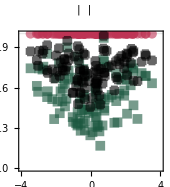

```mathematica
cross=Graphics[{Thickness[0.3],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];
leg=Multicolumn[{PointLegend[{magentaviva},{MaTeX["\\frac{\\sigma_\\text{ti}}{\\sigma}",FontSize->15]},LegendMarkers->(mark[[1]]),Spacings->0],
PointLegend[{castletongreen},{MaTeX["\\frac{\\sigma_\\text{zk}}{\\sigma}",FontSize->15]},LegendMarkers->(mark[[2]]),Spacings->0],PointLegend[{Black},{MaTeX["\\frac{\\sigma_\\text{so}}{\\sigma}",FontSize->15]},LegendMarkers->(cross),Spacings->0]},3,Spacings->{0,-1.5}];
plotDDEPR2=Show[
ListPlot[{#1,#4/#3}&@@@vec,PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],10}],
ListPlot[{#1,#5/#3}&@@@vec,PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],10}],
ListPlot[{#1,(#4+#6)/(2#3)}&@@@vec,PlotStyle->{Black,Opacity[.6]},PlotMarkers->{cross,10}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.45,1.15}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-4,4},{0,1}},ImagePadding->{{20,20},{40,42}},PlotRangeClipping->False,GridLines->{{},{1}},GridLinesStyle->{Black}]
```

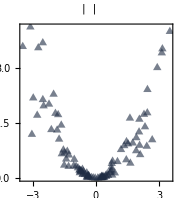
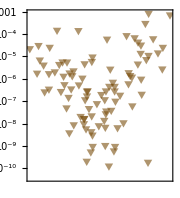
{-Graphics-,-Graphics--Graphics-}

```mathematica
size=180;ar=1.1;
leg2=Multicolumn[{PointLegend[{pageantblue},{MaTeX["D_x",FontSize->15]},LegendMarkers->(mark[[4]]),Spacings->0],
PointLegend[{sepia},{MaTeX["D_t",FontSize->15]},LegendMarkers->(mark[[5]]),Spacings->0]},3,Spacings->{0,-1.5}];
plot1=ListPlot[{#1,#7}&@@@vec,PlotStyle->{pageantblue,Opacity[.6]},PlotMarkers->{mark[[4]],10},ImagePadding->{{20,30},{40,25}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg2,Scaled[{.45,1.1}]]},PlotRangeClipping->False];
plot2=ListLogPlot[{#1,#8 }&@@@vec,PlotStyle->{sepia,Opacity[.6]},PlotMarkers->{mark[[5]],10},ImagePadding->{{20,30},{40,25}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""}];
plotDDD2=Overlay[{plot1,plot2}];
{plotDDEPR2,plotDDD2}
```

```mathematica
Export["plot_DD_EPR_2.png",plotDDEPR2,"PNG",ImageResolution->800]
Export["plot_DD_Dxt_2.png",plotDDD2,"PNG",ImageResolution->800]
```

plot_DD_EPR_2.png

plot_DD_Dxt_2.png

## DQD with distinct temperatures

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec={};Do[
{β1,β2,β3,β4}={1,x,1,1};
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

AppendTo[vec,Chop@{β2-β1,A34,σ,σzk}];
,{x,0.0,31,.02}]
```

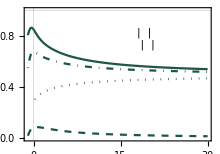

```mathematica
leg=Multicolumn[{LineLegend[{Dashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(1)}/\\sigma",FontSize->12]},LegendMarkerSize->22],LineLegend[{Dotted,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(2)}/\\sigma",FontSize->12]},LegendMarkerSize->22],
LineLegend[{DotDashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(3)}/\\sigma",FontSize->12]},LegendMarkerSize->22],
LineLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{(4)}/\\sigma",FontSize->12]},LegendMarkerSize->22]},3,Spacings->{0,-1}];
plotDDEPRnoniso=Show[
ListLinePlot[{#1,Total[#4[[;;2]]]/#3}&@@@vec,PlotStyle->{castletongreen,Dashed}],
ListLinePlot[{#1,Total[#4[[;;4]]]/#3}&@@@vec,PlotStyle->{castletongreen,Dotted}],
ListLinePlot[{#1,Total[#4[[;;6]]]/#3}&@@@vec,PlotStyle->{castletongreen,DotDashed}],
ListLinePlot[{#1,Total[#4[[;;8]]]/#3}&@@@vec,PlotStyle->{castletongreen}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\beta_2 - \\beta_1",FontSize->12],""},Epilog->{Inset[leg,Scaled[{.65,.77}]]},ImageSize->220,AspectRatio->.7,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{All,{0,1}},ImagePadding->{{17,5},{40,5}},GridLines->{{0},{1}}]
```

```mathematica
Export["plot_DD_EPR_noniso.png",plotDDEPRnoniso,"PNG",ImageResolution->700]
```

plot_DD_EPR_noniso.png

```mathematica
vec2={};Do[
{β1,β2,β3,β4}={1,x,1,1};
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,Xspace,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*observing reservoir 1*)
trans1={x1plus,x1minus};
Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,trans1,R][x1,x2]Px[pss,trans1,R][x1];
Px2rx1r=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]Px[pss,trans1,R][rev[x2]];
a=Px2Gx1[pss,trans1,R][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,trans1,R][x1,x2,t])/a//Simplify//Chop];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,trans1,R][rev[x2],rev[x1],t])/b//Simplify//Chop];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;2]]},{x2,Xspace[[;;2]]}];

AppendTo[vec2,Chop@{β2-β1,Dx,Dtt}];
,{x,0,2,.1}]
```

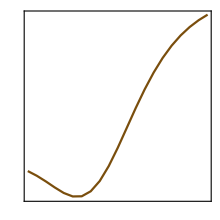
-Graphics--Graphics-

```mathematica
size=220;ar=1;
leg=Column[{LineLegend[{pageantblue,sepia},MaTeX[#,FontSize->14]&/@{"D_x","D_t"}]},Automatic,-.3];
plot1=ListLinePlot[{#1,#2}&@@@vec2,PlotStyle->pageantblue,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["\\beta_2 - \\beta_1",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.3,.77}]]}];
plot2=ListLinePlot[{#1,#3}&@@@vec2,PlotStyle->sepia,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["\\beta_2 - \\beta_1",FontSize->14],""}];
plotDDD=Overlay[{plot1,plot2}]
```

## Brusselator

### analytical approximation

The state space is truncated with a fixed N_max and all other calculations are analytical

```mathematica
Nmax=20;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={3,2,2,3,3,1};{A,B}={9,10};V=2;
```

Builiding the generator:

```mathematica
(*yp = +B, xp = -A, y = inner*)
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
ByteCount[Rsp]/10^6//N
```

0.051312

Stationary distribution

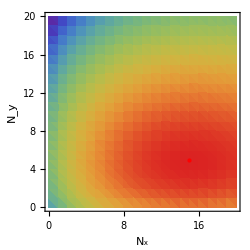
{-Graphics-,-Graphics3D-}

```mathematica
<<ComputationalGeometry`
pss=SteadyState[Rsp];
pssNxNy=Table[{Nx[Nmax][i],Ny[Nmax][i],pss[[i]]},{i,Length@pss}];
points={#1,#2}&@@@pssNxNy;zval=#3&@@@pssNxNy;
tri=DelaunayTriangulation[points];
tests=And@@Thread[zval[[#1]]>zval[[#2]]]&@@@tri;
maxima=Pick[points,tests];
{ListDensityPlot[ArrayFlatten[{{points,List/@zval}}],Epilog->{Red,PointSize[Large],Point[maxima]},PlotRange->All,ImageSize->250,FrameStyle->Black,FrameLabel->{"N_x","N_y"},ColorFunction->"Rainbow",ScalingFunctions->{None,None,"Log"}],ListPlot3D[pssNxNy,PlotRange->All,AxesLabel->{"N_x","N_y","p_st"},ImageSize->300,AxesStyle->Black]}
```

Defining the multifilar events

```mathematica
(*yp = +B, xp = +A, y = inner*)
xAplus={#1[[2]],#1[[1]],#2}&@@@rulexp;xAminus={#1[[2]],#1[[1]],#2}&@@@rulexm;rev[xAplus]=xAminus;rev[xAminus]=xAplus;
xBplus={#1[[2]],#1[[1]],#2}&@@@ruleyp;xBminus={#1[[2]],#1[[1]],#2}&@@@ruleym;rev[xBplus]=xBminus;rev[xBminus]=xBplus;
xIplus={#1[[2]],#1[[1]],#2}&@@@ruley;xIminus={#1[[2]],#1[[1]],#2}&@@@rulex;rev[xIplus]=xIminus;rev[xIminus]=xIplus;
Xspace={xAplus,xAminus,xBplus,xBminus,xIplus,xIminus};
transitions=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}],Transpose[{xIplus,xIminus}]];
Ssp=Smatrix[Rsp,transitions];
Z=Kfun[transitions,pss];
σ=EPR[Rsp,transitions];
```

The estimator σ_zk when chemostats A and B are monitored:

```mathematica
(*from A and B*)
transAB=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}]];
Ssp=Smatrix[Rsp,transAB];
Z=Kfun[transAB,pss];
σzk=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace[[;;4]]];
σzkB=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace[[3;;4]]];
{Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N,σ,σzk,σzkB}
```

{0.393043,1.6354,1.60214,0.970521}

The detector D_x

```mathematica
(*observing chemostats A and B*)
trans1={xAplus,xAminus,xBplus,xBminus};
Dx=0;
Do[
Px1x2=Px2Gx1[pss,trans1,Rsp][x1,x2]Px[pss,trans1,Rsp][x1];
Px2rx1r=Px2Gx1[pss,trans1,Rsp][rev[x2],rev[x1]]Px[pss,trans1,Rsp][rev[x2]];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
,{x1,Xspace[[;;4]]},{x2,Xspace[[;;4]]}];
Dx
```

0.0354987

```mathematica
Plα=Kfun[{xAminus},pss]/Kfun[transitions,pss] Kfun[{xIplus},pss]Kfun[{xBplus},pss]Total[Γmatrix[xIplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xBplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xAminus,pss].pss];
Plαr=Kfun[{xIminus},pss]/Kfun[transitions,pss] Kfun[{xAplus},pss]Kfun[{xBminus},pss]Total[Γmatrix[xAplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xBminus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xIminus,pss].pss];
{Δμ,Log[Plα/Plαr]}
```

{0.393043,0.393043}

### plot from simulation data

```mathematica
data=Import["bruss_simulation_results.txt","Table"];
```

```mathematica
(*aff_mean,epr_mean,epr_std,σzkB_mean,σzkB_std,σzk_mean,σzk_std,σti_mean,σti_std,Dx_mean,Dx_std,Dt_mean,Dt_std*)
```

```mathematica
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->12]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->12]},LegendMarkers->(mark[[1]])],PointLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{A,B}",FontSize->12]},LegendMarkers->(mark[[2]])]},1,Spacings->{0,-1}];
plotBrussEPR=Show[{ListLinePlot[{#1,#2}&@@@data,PlotStyle->Black],
ListPlot[{#1,Around[#8,#9]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],11}],
ListPlot[{#1,Around[#6,#7]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],11}]},
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->12],""},Epilog->{Inset[leg,Scaled[{.6,.7}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-.42,.42},All},ImagePadding->{{25,5},{40,5}}]
```

-Graphics-

```mathematica
leg=Column[{PointLegend[{pageantblue},{MaTeX["D_x",FontSize->12]},LegendMarkers->(mark[[1]])],PointLegend[{sepia},{MaTeX["D_t",FontSize->12]},LegendMarkers->(mark[[2]])]},Automatic,-.3];
plotBrussD=Show[{ListLinePlot[{#1,Around[#10,#11]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{pageantblue,Opacity[.6]},PlotMarkers->{mark[[1]],11}],ListLinePlot[{#1,Around[#12,#13]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{sepia,Opacity[.6]},PlotMarkers->{mark[[2]],11}]},Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->12],""},Epilog->{Inset[leg,Scaled[{.6,.8}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-.42,.42},All},ImagePadding->{{25,5},{40,5}}]
```

-Graphics-

```mathematica
Export["plot_Bruss_EPR.png",plotBrussEPR,"PNG",ImageResolution->600]
Export["plot_Bruss_Dxt.png",plotBrussD,"PNG",ImageResolution->600]
```

### randomized

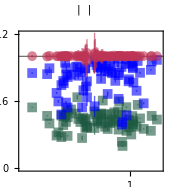

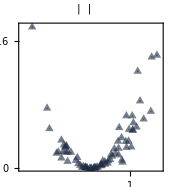
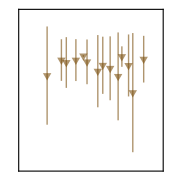

```mathematica
(*[Δμ, epr_mean, epr_std, σzk_mean, σzk_std, σzkA_mean, σzkA_std, σti1s_mean, σti1s_std, σti2s_mean, σti2s_std, σti3s_mean, σti3s_std, σwtA_mean, σwtA_std, DxA_mean, DxA_std, DtA_mean, DtA_std, σwt_mean, σwt_std, Dx_mean, Dx_std, Dt_mean, Dt_std, epr_exact ]*)
vec=Import["bruss_simu_final_2"];
vec2=SortBy[SortBy[vec,Abs[#[[1]]]&][[5;;-1;;1]],First];
leg=Multicolumn[{PointLegend[{magentaviva},{MaTeX["\\frac{\\sigma_\\text{ti}}{\\sigma}",FontSize->15]},LegendMarkers->(mark[[1]]),Spacings->0],
PointLegend[{castletongreen},{MaTeX["\\frac{\\sigma_\\text{zk}^{\\text{(A)}}}{\\sigma}",FontSize->15]},LegendMarkers->(mark[[2]]),Spacings->0],PointLegend[{Blue},{MaTeX["\\frac{\\sigma_\\text{zk}^{\\text{(AB)}}}{\\sigma}",FontSize->15]},LegendMarkers->(mark[[2]]),Spacings->0]},3,Spacings->{0,-1.5}];
plotBrussEPR2=Show[
ListPlot[{#1,Around[#6/#2,1/#2 √(#7^2+(#6/#2)^2#3^2)]}&@@@vec2,PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],10}],
ListPlot[{#1,Around[#4/#2,1/#2 √(#5^2+(#4/#2)^2#3^2)]}&@@@vec2,PlotStyle->{Blue,Opacity[.6]},PlotMarkers->{mark[[2]],10}],
ListPlot[{#1,Around[Mean[{#8,#10,#12}]/#2,1/#2 √(((1/3)√(#9^2+#11^2+#13^2))^2+(Mean[{#8,#10,#12}]/#2)^2#3^2)]}&@@@vec2,PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],10}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.45,1.15}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-1.8,1.8},{0,1.2}},ImagePadding->{{20,20},{40,42}},PlotRangeClipping->False,GridLines->{{},{1}},GridLinesStyle->Black,FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][0,1.5],Automatic},{Charting`ScaledTicks["Linear","Nice"][-4,4],Automatic}}]
size=170;ar=1.1;
vec3=vec2[[2;;-1;;5]];
leg2=Multicolumn[{PointLegend[{pageantblue},{MaTeX["D_x",FontSize->15]},LegendMarkers->(mark[[4]]),Spacings->0],
PointLegend[{sepia},{MaTeX["D_t",FontSize->15]},LegendMarkers->(mark[[5]]),Spacings->0]},3,Spacings->{0,-1.5}];
plot1=ListPlot[{#1,Around[#16,#17]}&@@@vec,PlotStyle->{pageantblue,Opacity[.6]},PlotMarkers->{mark[[4]],10},ImagePadding->{{20,25},{40,25}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["\\Delta\\mu",FontSize->14],""},Epilog->{Inset[leg2,Scaled[{.45,1.1}]]},PlotRangeClipping->False,PlotRange->{{-1.8,1.8},All},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][0,1.5],Automatic},{Charting`ScaledTicks["Linear","Nice"][-4,4],Automatic}}];
plot2=ListPlot[{#1,Around[#18,#19]}&@@@vec3,PlotStyle->{sepia,Opacity[.6]},PlotMarkers->{mark[[5]],10},ImagePadding->{{20,25},{40,25}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""},PlotRange->{{-1.8,1.8},{-.31,.12}}];
plotBrussD2=Overlay[{plot1,plot2}]
```

```mathematica
Export["plot_Bruss_EPR_2.png",plotBrussEPR2,"PNG",ImageResolution->800]
Export["plot_Bruss_Dxt_2.png",plotBrussD2,"PNG",ImageResolution->800]
```

plot_Bruss_EPR_2.png

plot_Bruss_Dxt_2.png

```mathematica
(*TEST IF ALL VALUES ARE IN [0,σ] UP TO 3 STANDARD DEVIATIONS *)
And@@(TrueQ[-3#2<=#1<=1+3#2]&@@@({#4/#2,1/#2 √(#5^2+(#4/#2)^2#3^2)}&@@@vec))(*σzk*)
And@@(TrueQ[-3#2<=#1<=1+3#2]&@@@({#6/#2,1/#2 √(#7^2+(#6/#2)^2#3^2)}&@@@vec))(*σzkA*)
And@@(TrueQ[-3#2<=#1<=1+3#2]&@@@({Mean[{#8,#10,#12}]/#2,1/#2 √(((1/3)√(#9^2+#11^2+#13^2))^2+(Mean[{#8,#10,#12}]/#2)^2#3^2)}&@@@vec))(*σti*)
And@@(TrueQ[-3#2<=#1<=1+3#2]&@@@({#14/#2,1/#2 √(#15^2+(#14/#2)^2#3^2)}&@@@vec))(*σsoA*)
And@@(TrueQ[-3#2<=#1<=1+3#2]&@@@({#20/#2,1/#2 √(#21^2+(#20/#2)^2#3^2)}&@@@vec))(*σsoA*)
```

True

True

True

«2 more identical outputs»

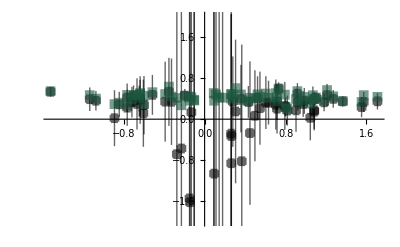

```mathematica
Show[ListPlot[{#1,Around[#14/#2,1/#2 √(#15^2+(#14/#2)^2#3^2)]}&@@@vec2,PlotStyle->{Black,Opacity[.6]},PlotMarkers->{cross,10},PlotRange->{All,{-2,2}}],ListPlot[{#1,Around[#6/#2,1/#2 √(#7^2+(#6/#2)^2#3^2)]}&@@@vec2,PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],10}]]
```

## Gershgorin circles

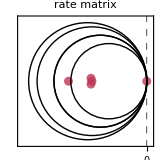
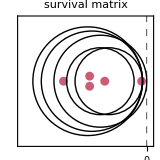

```mathematica
R={{0,1,2,3,4},{1,0,4,3,2},{5,4,0,3,2},{5,4,1,0,3},{3,4,2,2,0}}/10;
R=R-DiagonalMatrix[Total[R]];
S=R;(S[[#2,#1]]=0)&@@@{{1,2},{2,1},{3,4},{4,3}};
eigsR=Eigenvalues[R]//N;
eigsS=Eigenvalues[S]//N;
gcR=Table[{R[[i,i]],Total@Drop[R[[;;,i]],{i}]},{i,Length@R}];
gcS=Table[{S[[i,i]],Total@Drop[S[[;;,i]],{i}]},{i,Length@R}];

a=ListPlot[{Re[#],Im[#]}&/@eigsR,PlotStyle->{magentaviva,PointSize->.04,Opacity[0.8]},Epilog->((Circle[{#1,0},#2])&@@@gcR),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times"},PlotLabel->Style["rate matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
b=ListPlot[{Re[#],Im[#]}&/@eigsS,PlotStyle->{magentaviva,PointSize->.04,Opacity[0.8]},Epilog->((Circle[{#1,0},#2])&@@@gcS),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times"},PlotLabel->Style["survival matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
{a,b}
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["gershgorin_R.png",a,"PNG",ImageResolution->500]
Export["gershgorin_S.png",b,"PNG",ImageResolution->500]
```

gershgorin_R.png

gershgorin_S.png